BISECTION METHOD

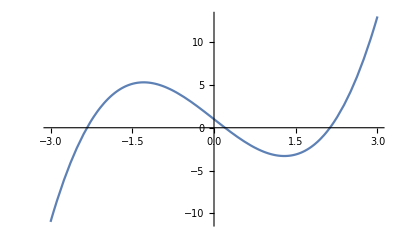

```mathematica
f[x_] := x^3 -5x +1
Plot[f[x] ,{x,-3,3}]
```

```mathematica
f[x_] := x^3 -5x +1
a[0]=0;
b[0]=1;
Do[p[n+1]=N[(a[n]+b[n])/2];
If[N[f[a[n]] f[p[n+1]]]<0,a[n+1]=a[n];
b[n+1]=p[n+1],a[n+1]=p[n+1];
b[n+1]=b[n]],{n,0,20}]
TableForm[Table[{n,a[n],b[n],p[n+1],f[p[n+1]]},{n,0,20}]]
```

0 | 0 | 1 | 0.5 | -1.375
1 | 0 | 0.5 | 0.25 | -0.234375
2 | 0 | 0.25 | 0.125 | 0.376953
3 | 0.125 | 0.25 | 0.1875 | 0.0690918
4 | 0.1875 | 0.25 | 0.21875 | -0.0832825
5 | 0.1875 | 0.21875 | 0.203125 | -0.00724411
6 | 0.1875 | 0.203125 | 0.195313 | 0.0308881
7 | 0.195313 | 0.203125 | 0.199219 | 0.0118129
8 | 0.199219 | 0.203125 | 0.201172 | 0.00228208
9 | 0.201172 | 0.203125 | 0.202148 | -0.0024816
10 | 0.201172 | 0.202148 | 0.20166 | -0.0000999043
11 | 0.201172 | 0.20166 | 0.201416 | 0.00109105
12 | 0.201416 | 0.20166 | 0.201538 | 0.000495564
13 | 0.201538 | 0.20166 | 0.201599 | 0.000197827
14 | 0.201599 | 0.20166 | 0.20163 | 0.000048961
15 | 0.20163 | 0.20166 | 0.201645 | -0.0000254717
16 | 0.20163 | 0.201645 | 0.201637 | 0.0000117446
17 | 0.201637 | 0.201645 | 0.201641 | -6.86358×10^-6
18 | 0.201637 | 0.201641 | 0.201639 | 2.44052×10^-6
19 | 0.201639 | 0.201641 | 0.20164 | -2.21153×10^-6
20 | 0.201639 | 0.20164 | 0.20164 | 1.14493×10^-7